# The Chess Package

Load the package:

```mathematica
Needs["Chess`"]
```

## Pieces and moves

Pieces includes all pieces, including the virtual pieces piece0 and piece33:

```mathematica
{piece0,piece33}
```

{<|id→0,image→{},status→enpassant,pos→{{}}|>,<|id→33,image→{},status→enpassant,pos→{{}}|>}

The properties of each piece is embedded in the association piece#, where # is the piece number.

The image of each piece is downloaded or kept in the mx-file pieceImages.mx:

```mathematica
GraphicsGrid[Partition[#[image]&/@Most@Rest@Pieces,16],ImageSize->500]
```

-Graphics-

Standard positions are obtained by executing Startposition:

```mathematica
Startposition
```

whiteoptionlist and blackoptionlist display move options of all pieces by x- and y-coordinates:

```mathematica
whiteoptionlist
```

<|1→{{1,3},{1,4}},2→{{2,3},{2,4}},3→{{3,3},{3,4}},4→{{4,3},{4,4}},5→{{5,3},{5,4}},6→{{6,3},{6,4}},7→{{7,3},{7,4}},8→{{8,3},{8,4}},9→{{1,3},{3,3}},10→{{6,3},{8,3}}|>

```mathematica
blackoptionlist
```

<|17→{{1,6},{1,5}},18→{{2,6},{2,5}},19→{{3,6},{3,5}},20→{{4,6},{4,5}},21→{{5,6},{5,5}},22→{{6,6},{6,5}},23→{{7,6},{7,5}},24→{{8,6},{8,5}},25→{{1,6},{3,6}},26→{{6,6},{8,6}}|>

A move may be selected randomly by RandomMove:

```mathematica
move1=RandomMove
```

{1,{1,3}}

The status of this piece number is

```mathematica
#[status]&/@Select[Pieces,#[id]===move1[[1]]&]
```

{pawn}

and the move is to

```mathematica
Coord[move1[[2]]]
```

a3

The function Move is used to move the piece:

```mathematica
Move[move1]
```

The situation after the move is displayed by Chess[]:

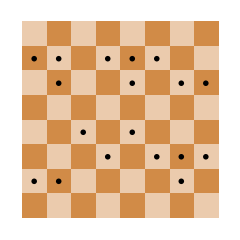

```mathematica
Chess[]
```

Next move could also be randomly found, this time black is to move:

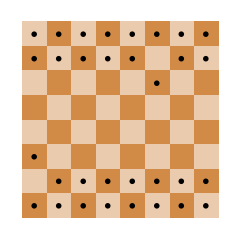

```mathematica
Move[RandomMove];Chess[]
```

And so on ...

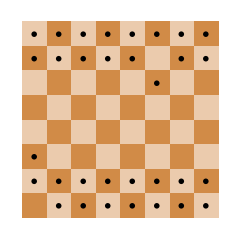

```mathematica
Move[RandomMove];Chess[]
```

## Options

The options regulate how the chessboard should be displayed

```mathematica
Options[Chess]//TableForm
```

ShowBoard→Static
ImageSize→240
PieceSize→Automatic
BoardColour→RGBColor[0.8196, 0.5451, 0.2784]
ShowPieces→All
PawnConvert→MakeQueen
ShowPGN→True
Interact→True

### ShowPieces

ShowPieces may have three values

All - All pieces are displayed (default)

White - Only the white pieces are shown

Black - Only the black pieces are shown

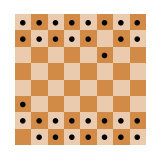
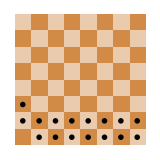
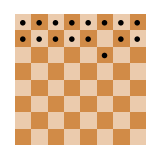

```mathematica
Chess[ShowPieces->#,ImageSize->160]&/@{All,White,Black}
```

### PawnConvert

PawnConvert may have two values

MakeQueen - pawns are converted to queens (default)

Menu - pawns are converted according to interactive choices (not working!!)

### ShowBoard

ShowBoard could have the following values :

None - No chessboard is displayed

Static - The chessboard is displayed with current placement of pieces (default value)

Dynamic - Pieces are allowed to move as they change positions

Random - Pieces can be randomly moved by clicking the displayed buttons

PGN-values - Pieces are moved according to predefined PGN-values

```mathematica
Startposition;
Chess[ShowBoard->Dynamic]
Do[Move[RandomMove];Pause[.3],{10}]
```

```mathematica
Startposition;
Chess[ShowBoard->Interactive]
```

```mathematica
Chess[ShowBoard->Random,ShowPGN->False]
```

RestartBackRandom Move

## Display PGN moves

```mathematica
alekhine=Import["http://chessproblem.my-free-games.com/PGN/Alekhine.zip","*.pgn"][[1]];
```

```mathematica
MakePGNfiles[alekhine]
```

2408 PGN files are available (PGNfile[no])

```mathematica
PGNfile[2000]
```

<|Event→World Ch.,Site→Buenos Aires ARG,Date→1927.??.??,Round→18,White→Alekhine, Alexander A,Black→Capablanca, Jose Raul,Result→1/2-1/2,ECO→D67,PGN→{1.d4,Nf6,2.c4,e6,3.Nc3,d5,4.Bg5,Nbd7,5.e3,Be7,6.Nf3,O-O,7.Rc1,c6,8.Bd3,dxc4,9.Bxc4,Nd5,10.Bxe7,Qxe7,11.Ne4,N5f6,12.Ng3,Qb4+,13.Qd2,Qxd2+,14.Kxd2,Rd8,15.Ke2,b6,16.Rhd1,Bb7,17.Rd2,Kf8,18.Rcd1,Ke7,19.e4,h6,20.h3,g6,21.Rd3,c5,22.dxc5,Nxc5,23.Rxd8,Rxd8,24.Rxd8,Kxd8,25.Ne5,Ke7,26.f3,Nfd7,27.Nxd7,Nxd7,28.Kd3}|>

```mathematica
pgn=PGNconvert[PGNfile[2000]["PGN"]]
```

{{4,4},{knight,6,6},{3,4},{5,6},{knight,3,3},{4,5},{bishop,7,5},{knight,b,4,7},{5,3},{bishop,5,7},{knight,6,3},{0,Chess`Private`short},{rook,3,1},{3,6},{bishop,4,3},{d,x,3,4},{bishop,x,3,4},{knight,4,5},{bishop,x,5,7},{queen,x,5,7},{knight,5,4},{knight,5,6,6},{knight,7,3},{queen,2,4},{queen,4,2},{queen,x,4,2},{king,x,4,2},{rook,4,8},{king,5,2},{2,6},{rook,h,4,1},{bishop,2,7},{rook,4,2},{king,6,8},{rook,c,4,1},{king,5,7},{5,4},{8,6},{8,3},{7,6},{rook,4,3},{3,5},{d,x,3,5},{knight,x,3,5},{rook,x,4,8},{rook,x,4,8},{rook,x,4,8},{king,x,4,8},{knight,5,5},{king,5,7},{6,3},{knight,f,4,7},{knight,x,4,7},{knight,x,4,7},{king,4,3}}

```mathematica
Chess[ShowBoard->pgn,Interact->False]
```

RestartBackNextEnd

```mathematica
PGN//Dynamic
```